## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/reduction/";  Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.27877 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Apr 18, 2020, time: 23:59:58

nb: /Users/dantopa/Mathematica_files/nb/ert/rcs/reduction/acucmulation-plot.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.27877 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

#### functions

#### substitutions

#### modules

## data

### import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
σ=RotateLeft[meanRCS,180];
{m,n}=Dimensions[σ]
```

{28,361}

### plot

```mathematica
θticks={{1,"-180°"},{91,"-90°"},{181,"0°"},{271,"90°"},{361,"180°"}};
```

```mathematica
fticks={{Automatic,Automatic},{θticks,Automatic}};
```

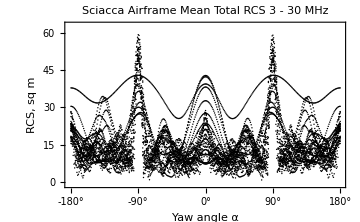

```mathematica
gnew=ListPlot[σ,
isize,
Frame->True,
FrameTicks->fticks,
PlotRange->{Automatic,{-1,63}},
FrameLabel->{"Yaw angle α","RCS, sq m"},
PlotLabel->"Sciacca Airframe"<>lf<>"Mean Total RCS 3 - 30 MHz",
Joined->False,
PlotStyle->Black]
```

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

59.2522

0.798997

```mathematica
tresExport["rcs-all-frequencies",gnew]
```

## 1

```mathematica
gnew=ListPlot[Drop[σ,0],
isize,
Frame->True,
FrameTicks->fticks,
PlotRange->{Automatic,{-1,63}},
FrameLabel->{"Yaw angle α","RCS, sq m"},
PlotLabel->"Sciacca Airframe"<>lf<>"Mean Total RCS 3 - 30 MHz",
Joined->False,
PlotStyle->Black]
```

-Graphics-

## 2

```mathematica
Dimensions[σ]
```

{28,361}

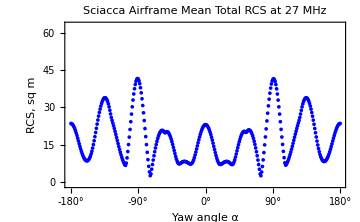

```mathematica
ν=27;
index=ν-2;
gnew=ListPlot[σ[[index]],
isize,
Frame->True,
FrameTicks->fticks,
PlotStyle->Blue,
PlotRange->{Automatic,{-1,63}},
FrameLabel->{"Yaw angle α","RCS, sq m"},
PlotLabel->"Sciacca Airframe"<>lf<>"Mean Total RCS at "<>ToString[ν]<>" MHz",
Joined->False,
PlotStyle->Black]
```

## ascend

```mathematica
title="Sciacca Airframe"<>lf;
Do[
tag="30 MHz";
If[k>1,tag="30 - "<>ToString[30-k]<>" MHz"];
plabel=title<>tag;
gnew=ListPlot[σ[[1;;k]],
isize,
Frame->True,
FrameTicks->fticks,
PlotStyle->Blue,
PlotRange->{Automatic,{-1,63}},
FrameLabel->{"Yaw angle α","RCS, sq m"},
PlotLabel->plabel,
Joined->False,
PlotStyle->Black];
Export[dirGraph<>"descending-"<>pad[k]<>".png",gnew];
,{k,Length[σ]}]
```

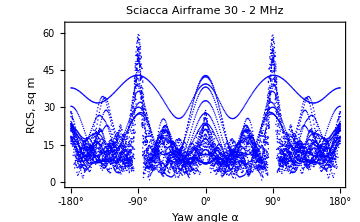

```mathematica
Show[gnew]
```

## visual index

```mathematica
Do[
g=ListPlot[σ[[k]],
isize,
Frame->True,
FrameTicks->fticks,
PlotStyle->Blue,
PlotRange->{Automatic,{-1,63}},
FrameLabel->{"Yaw angle α","RCS, sq m"},
PlotLabel->"Sciacca Airframe"<>lf<>"Mean Total RCS entry "<>ToString[k],
Joined->False,
PlotStyle->Black];
Export[dirGraph<>"probe-"<>pad[k]<>".png",g]
,{k,Length[σ]}];
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```